## 1 SN/Hopf, other

```mathematica
plots={};
discr1=(8α+α^2+2α μ2+μ2^2);
discr2=(-8α+α^2-2α μ2+μ2^2);
solns=Solve[(
discr1/.{α->Sqrt[μ3]}
)==0,μ3];
For[i=1,i≤2,i++,
pl=Plot[μ3/.solns[[i]],{μ2,-8,8},PlotStyle->{Red,Blue}[[i]]];
AppendTo[plots,pl];
]
solns=Solve[(
discr2/.{α->Sqrt[μ3]}
)==0,μ3];
For[i=1,i≤2,i++,
pl=Plot[μ3/.solns[[i]],{μ2,-8,8},PlotStyle->{Green,Yellow}[[i]]];
AppendTo[plots,pl];
]


uu2={-5,-1,1,5};
uu3={1,2,6};
For[i=1,i≤Length[uu2],i++,
For[j=1,j≤Length[uu3],j++,
u2=uu2[[i]];
u3=uu3[[j]];
replacements={μ2->u2,μ3->u3};
d1=discr1/.α->Sqrt[μ3]/.replacements//N;
d2=discr2/.α->Sqrt[μ3]/.replacements//N;
If[d1≥0,d1stat="+",d1stat="-"];
If[d2≥0,d2stat="+",d2stat="-"];
AppendTo[plots,scatter[{u2},{u3},Black,StringForm["``,``",d1stat,d2stat]]
];
]
]
```

```mathematica
scatter[xlist_,ylist_,color_,marker_]:=
(
data=Transpose@{xlist,ylist};
Return[ListPlot[
data,
PlotStyle->{PointSize[Large],color},
PlotMarkers->{marker,12},
AxesLabel->{"x","y"}
]];
);
```

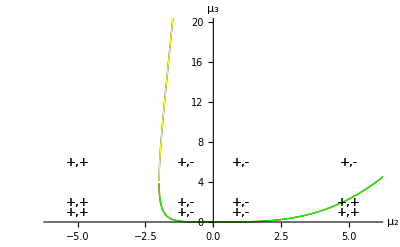

```mathematica
Show[plots,PlotRange->{{-6,6},{0,20}},AxesLabel->{"μ_2","μ_3"}]
```

## u,v form

```mathematica
uvsoln=Solve[{v==0,0==ν1+u^2+ϵ(ν2 v+u v)},{u,v}]
```

{{u→-ⅈ √ν1,v→0},{u→ⅈ √ν1,v→0}}

```mathematica
soln=u/.uvsoln/.ν1->N1
```

{-ⅈ √N1,ⅈ √N1}

Level sets of the V(u, v) function given (for ν_1=-1<0, when there are real fixed points):

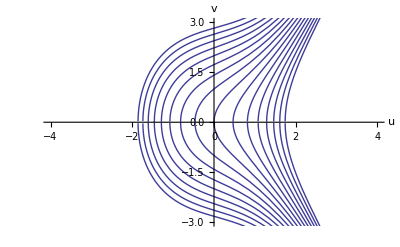

```mathematica
plots={};
N1=1;
For[i=1,i≤16,i++,
K=(Range[16][[i]]-8)/2;
levelSoln=Solve[k==v^2/2-ν1 u-u^3/3/.ν1->N1/.k->K,v];
AppendTo[plots,Plot[v/.levelSoln,{u,-6,6},AxesLabel->{"u","v"}]];
usoln=u/.uvsoln/.ν1->N1;
vsoln=v/.uvsoln/.ν1->N1;
AppendTo[plots,scatter[usoln,vsoln,Black,Automatic]];
];
Show[plots,PlotRange->{{-4,4},{-3,3}}]
```

Fixed points come nearer together until they collide and disppear, reminiscent of a S/N bifurcation.

Jacobian of the u/v version :

```mathematica
J=D[{v,ν1+u^2+ϵ(ν2 v+u v)},{{u,v}}];
TraditionalForm[MatrixForm[J]]
```

(0 | 1
2 u+v ϵ | ϵ (ν2+u))

Eigenvalues in the right half of the ν_3 × ν_2 plane (red is real; blue is imaginary):

```mathematica
smalleps={ϵ->.9};
For[i=1,i≤2,i++,
U={-Sqrt[ν3],Sqrt[ν3]}[[i]];
eigs=Simplify[Eigenvalues[J]]/.{u->U,v->0};
re=Re[eigs/.smalleps];
im=Im[eigs/.smalleps];
Print["at the fixed point",{U,0}];
Print[{Plot3D[{re[[1]],im[[1]]},{ν2,-16,16},{ν3,0,16},PlotStyle->{Red,Blue},AxesLabel->{"ν_2","ν_3","λ_1"},ImageSize->Medium],
Plot3D[{re[[2]],im[[2]]},{ν2,-16,16},{ν3,0,16},PlotStyle->{Red,Blue},AxesLabel->{"ν_2","ν_3","λ_2"},ImageSize->Medium]}];
];
```

at the fixed point{-√ν3,0}

{-Graphics3D-,-Graphics3D-}

at the fixed point{√ν3,0}

{-Graphics3D-,-Graphics3D-}